```mathematica
Dynamical Systems TIF155/FIM770
Konstantinos Zakkas
Problem set 2
```

```mathematica
2.4 Homoclinic bifurcation
```

```mathematica
xDot[x_, y_, μ_] := μ x+y−x^2;
yDot[x_,y_,μ_]:=-x+μ y +2 x^2;
FPs = Solve[{xDot[x,y,μ]==0, yDot[x,y,μ]==0},{x,y}]
```

{{x→0,y→0},{x→(1+μ^2)/(2+μ),y→(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}}

```mathematica
(*Using different values for mu we check the stability and the value of mu which gives a homoclinic bifurcation is μ=0.066*)
μ=0.066;
t0 = 0;
tmax = 300;
x0= (x/.FPs[[2]])-0.005;
y0= (y/.FPs[[2]]);
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ],x[0]==x0, y[0]==y0},{x[t],y[t]},{t,t0,tmax}];
 
p0 = ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tmax},PlotRange->{{-1,1},{-1,1}},PlotLabel->StringForm["μ=``",μ] ,PlotStyle->{Thick, Blue}]/.Line[x_]:>{Arrowheads[{0.05,{0.05,0.4},{0.05,0.2},{0.05,0.1}}],Arrow[x]};
p1 = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}, StreamStyle->Gray, StreamColorFunction->None];
p3 = Graphics[{Red,Circle[Evaluate[{x,y}]/.FPs[[1]],0.02]}];
p4 = Graphics[{Red,Circle[Evaluate[{x,y}]/.FPs[[2]],0.02]}];Show[p0,p1, p3, p4]
```

```mathematica
μ=0.066
```

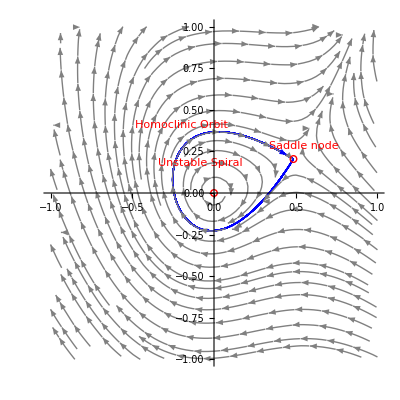

```mathematica
b)
```

```mathematica
μ=-0.066;
t0 = 0;
tmax = 300;
x0= (x/.FPs[[2]])-0.005;
y0= (y/.FPs[[2]]);
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ],x[0]==x0, y[0]==y0},{x[t],y[t]},{t,t0,tmax}];
 
p0 = ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tmax},PlotRange->{{-1,1},{-1,1}},PlotLabel->StringForm["μ=``",μ], PlotStyle->{Thick, Blue}]/.Line[x_]:>{Arrowheads[{{0.05,0.4},{0.05,0.2},{0.05,0.1}}],Arrow[x]};
p1 = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}, StreamStyle->Gray, StreamColorFunction->None];Show[p0,p1]
```

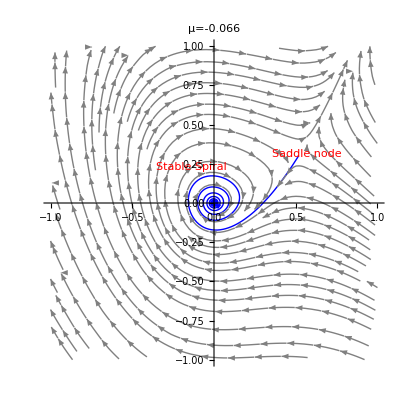

```mathematica
μ=0;
t0 = 0;
tmax = 50;
x0= (x/.FPs[[2]])-0.005;
y0= (y/.FPs[[2]]);
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ],x[0]==x0, y[0]==y0},{x[t],y[t]},{t,t0,tmax}];
 
p0 = ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tmax},PlotRange->{{-1,1},{-1,1}}, PlotLabel->StringForm["μ=``",μ],PlotStyle->{Thick, Blue}]/.Line[x_]:>{Arrowheads[{{0.05,0.4},{0.05,0.2},{0.05,0.1}}],Arrow[x]};
p1 = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}, StreamStyle->Gray, StreamColorFunction->None];Show[p0,p1]
```

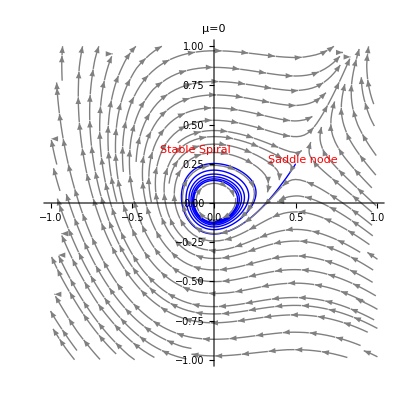

```mathematica
μ=0.06;
t0 = 0;
tmax = 300;
x0= (x/.FPs[[2]])-0.005;
y0= (y/.FPs[[2]]);
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ],x[0]==x0, y[0]==y0},{x[t],y[t]},{t,t0,tmax}];
 
p0 = ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tmax},PlotRange->{{-1,1},{-1,1}}, PlotLabel->StringForm["μ=``",μ],PlotStyle->{Thick, Blue}]/.Line[x_]:>{Arrowheads[{{0.05,0.3},{0.05,0.2},{0.05,0.1}}],Arrow[x]};
p1 = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}, StreamStyle->Gray, StreamColorFunction->None];Show[p0,p1]
```

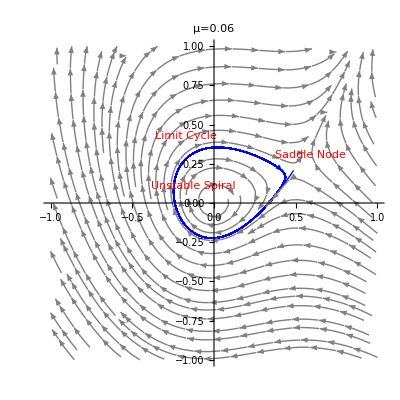

```mathematica
μ=0.07;
t0 = 0;
tmax = 300;
x0= (x/.FPs[[2]])-0.005;
y0= (y/.FPs[[2]]);
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ],x[0]==x0, y[0]==y0},{x[t],y[t]},{t,t0,tmax}];
 
p0 = ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tmax},PlotRange->{{-1,1},{-1,1}},PlotLabel->StringForm["μ=``",μ], PlotStyle->{Thick, Blue}]/.Line[x_]:>{Arrowheads[{{0.05}}],Arrow[x]};
p1 = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}, StreamStyle->Gray, StreamColorFunction->None];Show[p0,p1]
```

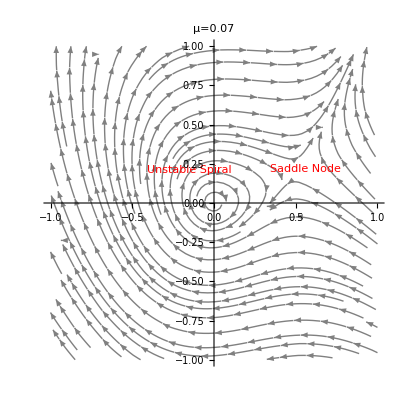

```mathematica
c)
```

```mathematica
sols = DSolve[{x'[t]==u x[t],y'[t]==s y[t],x[0]==γ,y[0]==1},{x[t],y[t]},t]
Solve[(x[t]/.Part[sols,1,1])== 1, t]
```

{{x[t]→ⅇ^(t u) γ,y[t]→ⅇ^(s t)}}

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[1/γ])/u, C[1]∈ℤ]}}

```mathematica
d)
```

```mathematica
μ=.
saddlex = x/.Part[FPs,2,1]
```

(1+μ^2)/(2+μ)

```mathematica
jacobianMatrix = {{μ-2saddlex,1},{-1+4saddlex,μ}};
eigenValues = Eigenvalues[jacobianMatrix]
```

{(-1+2 μ-√(5+9 μ^2+4 μ^3+μ^4))/(2+μ),(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)}

```mathematica
Part[eigenValues,2]//Simplify
```

(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)